# Notebook 09: The Manipulate Command

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## The Manipulate command

Mathematica has an extremely useful command called Manipulate, which makes it easy to build interactive interfaces.

Here is an example where we draw 50 randomly placed large orange points against a light blue background.

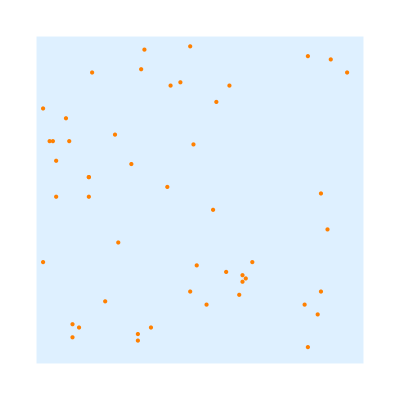

```mathematica
Graphics[{LightBlue,Rectangle[{0,0},{100,100}],PointSize[Large],Orange,Point[Table[RandomInteger[98,2]+1,{50}]]}]
```

The first thing we do is create a function to draw a given number of points. We also store our background in a symbol.

```mathematica
background={LightBlue,Rectangle[{0,0},{100,100}]};
```

```mathematica
drawOrangePoints[n_]:=
{Orange,PointSize[Large],Point[Table[RandomInteger[98,2]+1,{n}]]}
```

Now we can draw our points against the background as follows

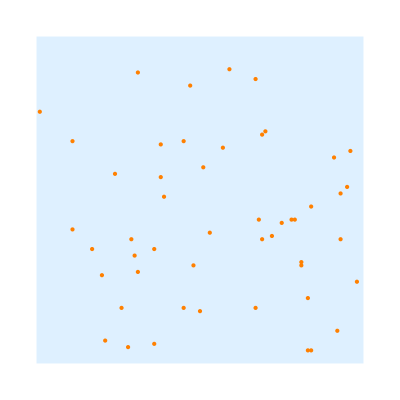

```mathematica
Graphics[{background,drawOrangePoints[50]}]
```

Now suppose we want to experiment with using more or fewer points. We set up a Manipulate command with our Graphics command inside of it. We replace the 50 with a variable (x in this case), then we add a list that looks just like the iterator from Table. In this case it says, allow x to vary from 50 to 500 in steps of 25.

```mathematica
Manipulate[Graphics[{background,drawOrangePoints[x]}],{x,50,500,25}]
```

Spend a few minutes experimenting with this: slide forward and back; step forward and back; animate forward, back and back and forth; increase and decrease animation speed.

## Simple animation with Manipulate

### A routine flight

One of the things we can do with Manipulate is use it to create simple animations.

```mathematica
drawPlane[{x_,y_}]:=
{Darker[Gray],Disk[{x,y},{10,1}],Rotate[Disk[{x-9,y+3/2},{2,1/2}],100 Degree],Rotate[Disk[{x,y},{5,1}],135Degree]}
```

```mathematica
Graphics[drawPlane[{0,0}],GridLines->Automatic,Frame->True]
```

-Graphics-

Here our plane flies smoothly across the sky.

```mathematica
Manipulate[Graphics[{background,drawPlane[{x,75}]}],{x,12,88}]
```

### Close encounter

Now suppose we add a UFO. If we want the UFO to move with the plane, we can use the same variable to control each.

```mathematica
drawUFO[{x_,y_}]:=
{Orange,Disk[{x,y},{6,2}],LightOrange,Disk[{x,y+1},{3,2}]}
```

```mathematica
Manipulate[Graphics[{background,drawPlane[{x,75}],drawUFO[{x-4,90}]}],{x,12,88}]
```

If we add some noise to the x and y positions of the UFO, we can get it to fly more erratically.

```mathematica
Manipulate[Graphics[{background,drawPlane[{x,75}],drawUFO[{x-RandomInteger[2],90+(RandomInteger[2]-1)}]}],{x,12,88}]
```

## Scanned by a UFO

Suppose we want our UFO to randomly ‘scan’ the plane. We start by making a cone-shaped beam of partially transparent light. We use an elliptical disk sector to round the bottom of the cone.

```mathematica
drawBeam[{x_,y_}]:=
{Opacity[1/2],Yellow,Polygon[{{x-2,y},{x+2,y},{x+10,y-18},{x-10,y-18}}],Disk[{x,y-18},{10,3/2},{180Degree,360 Degree}]}
```

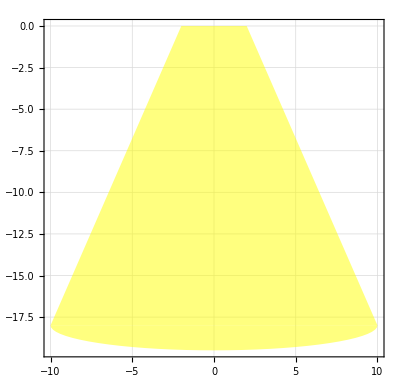

```mathematica
Graphics[drawBeam[{0,0}],GridLines->Automatic,Frame->True]
```

Then we create another drawing function that usually just draws the UFO, but sometimes draws the beam beneath it. We will give this function an argument p that allows us to control the probability of scanning.

```mathematica
drawScanningUFO[{x_,y_},p_]:=
{RandomChoice[{p,1-p}->{drawBeam[{x,y}],Point[{x,y}]}],drawUFO[{x,y}]}
```

By setting the probability to 1, we can see what it looks like with the beam.

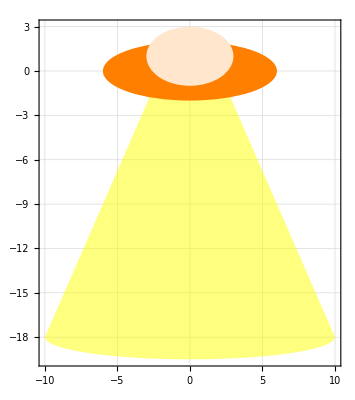

```mathematica
Graphics[drawScanningUFO[{0,0},1],GridLines->Automatic,Frame->True]
```

Here is the new animation, with the scanning probability set to 65%

```mathematica
Manipulate[Graphics[{background,drawPlane[{x,75}],drawScanningUFO[{x-RandomInteger[2],90+(RandomInteger[2]-1)},.65]}],{x,12,88}]
```

## Exporting animations

If we copy our Manipulate command and replace Manipulate with Table, we end up with a list of frames.

```mathematica
scanningUFOFrames=Table[Graphics[{background,drawPlane[{x,75}],drawScanningUFO[{x-RandomInteger[2],90+(RandomInteger[2]-1)},.65]}],{x,12,88}];
```

Here are the first 5 frames. This command shows a version of Part that allows us to see some elements of a list.

```mathematica
scanningUFOFrames⟦1;;5⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We can now use the Export command to create an animated GIF with these frames. To keep the animation short, I am only going to use the first 20 frames.

```mathematica
Export["scanningUFO.gif",scanningUFOFrames⟦1;;20⟧]
```

scanningUFO.gif

The file will be stored in your current working directory. Go out to your operating system and have a look at it.

```mathematica
Directory[]
```

/Users/wjt

## ListAnimate

We have just seen that we can use Table in place of Manipulate to create a list of frames. Here is a Manipulate and the equivalent list of frames we get when we replace the Manipulate with Table:

```mathematica
Manipulate[Graphics[{LightBlue,Rectangle[{0,0},{10,10}],Thick,Blue,Circle[{x,3},1]}],{x,1,9,2}]
```

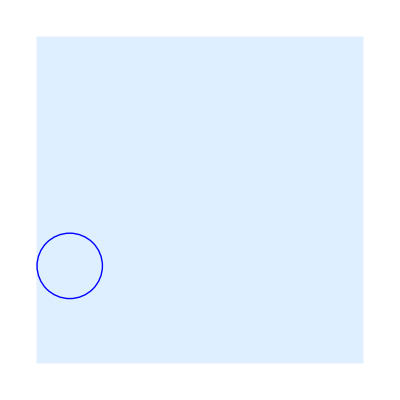
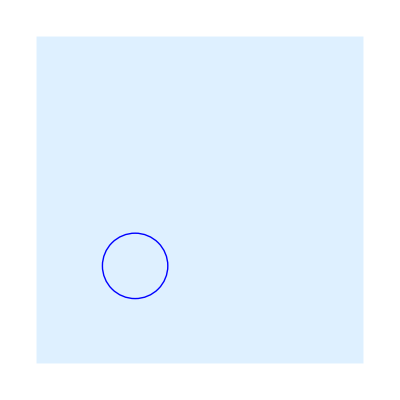
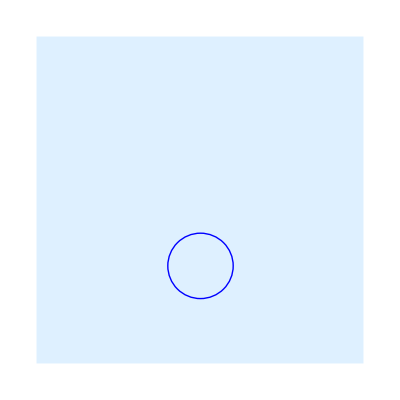
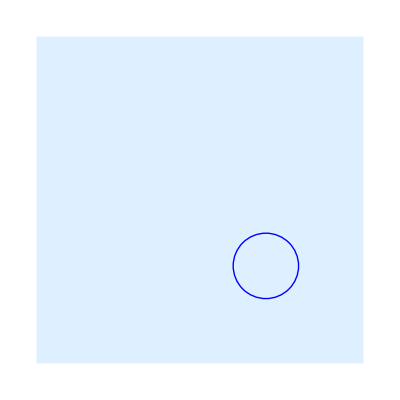
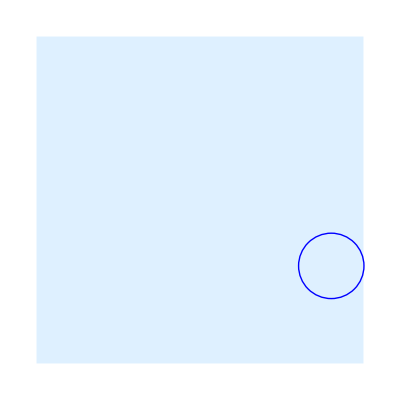

```mathematica
circleList=Table[Graphics[{LightBlue,Rectangle[{0,0},{10,10}],Thick,Blue,Circle[{x,3},1]}],{x,1,9,2}]
```

The ListAnimate command takes any such sequence of images and animates them. The second argument is how many frames per second we want the animation to play back at (one frame per second in this case).

```mathematica
ListAnimate[circleList,1]
```

## In-Class Activity

### Make an animated picture using the Graphics and Manipulate commands.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course